## Analysis of SimTree output

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/SimTree/source

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
colorlist={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

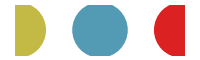

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,colorlist]},AspectRatio->0.3,ImageSize->200]
```

## Assumptions

Let’s say there are 10 sites that function to move the virus in phenotype space

```mathematica
10*0.005*(1/365)
```

0.000136986

Mutations per day

## World-wide SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

5.4795

```mathematica
popSize=data[[1,3]]
```

300000

### Prevalence

```mathematica
prev=data[[All,{1,5}]];
```

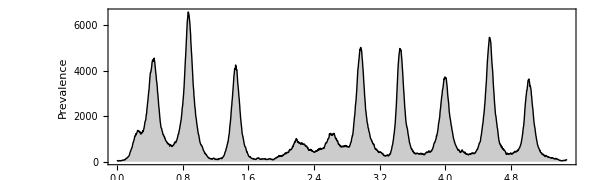

```mathematica
prevfig=ListLinePlot[prev,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Prevalence"},ImagePadding->{{40,10},{15,5}}]
```

### Incidence

```mathematica
inc=data[[All,{1,7}]];
```

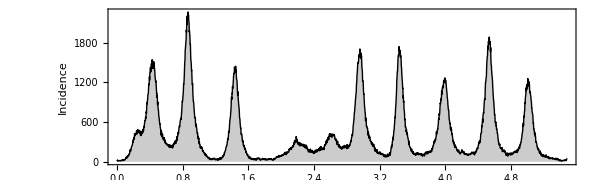

```mathematica
incfig=ListLinePlot[inc,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Incidence"},ImagePadding->{{40,10},{15,5}}]
```

Mean prevelance

```mathematica
N[Mean[prev[[All,2]]]]
```

1221.88

```mathematica
N[Mean[prev[[All,2]]]/popSize]
```

0.00407292

Mean incidence per year

```mathematica
N[(Total[inc[[All,2]]]/endTime)]
```

147674.

```mathematica
N[(Total[inc[[All,2]]]/endTime)/popSize]
```

0.492247

Flu incidence is 10% per year and prevalence is 0.14%.

### Diversity

```mathematica
div=data[[All,{1,2}]];
```

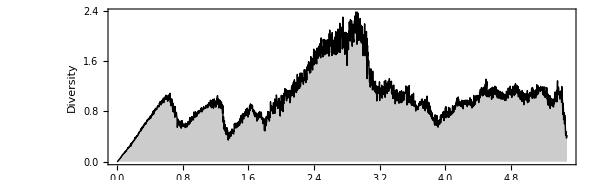

```mathematica
divfig=ListLinePlot[div,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Diversity"},ImagePadding->{{40,10},{15,5}}]
```

### Combined

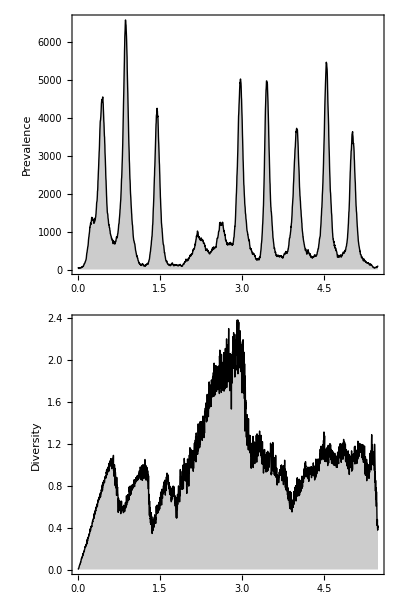

```mathematica
fig=Grid[{{prevfig},{divfig}}]
```

```mathematica
Export["timeseries.pdf",fig,"PDF"]
```

timeseries.pdf

## Regional SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

5.4795

### Prevalence

```mathematica
prevList={data[[All,{1,10}]],data[[All,{1,15}]],data[[All,{1,20}]]};
```

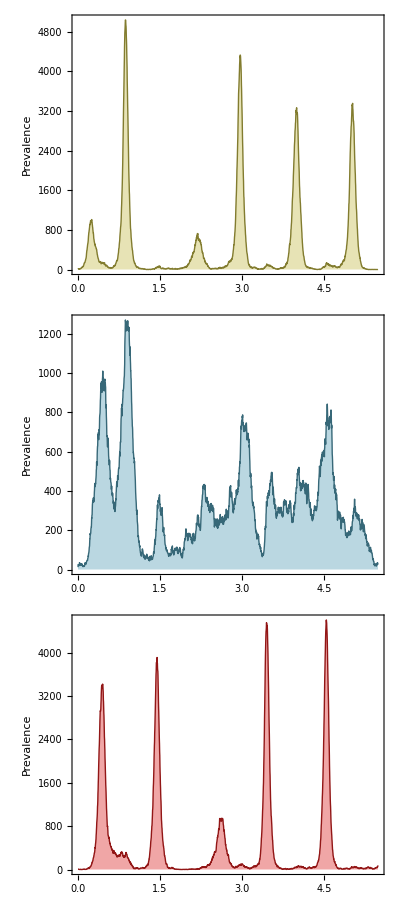

```mathematica
fig=Grid[Table[{ListLinePlot[prevList[[i]],AspectRatio->0.15,ImageSize->700,Filling->Axis,PlotStyle->Darker[colorlist[[i]]],FillingStyle->Directive[Opacity[0.4,colorlist[[i]]]],FrameLabel->{"","Prevalence"},ImagePadding->{{40,10},{15,5}}]},{i,3}]]
```

```mathematica
Export["spatialTimeseries.pdf",fig,"PDF"]
```

spatialTimeseries.pdf

## Tip traits

```mathematica
data=ToExpression[Import["out.tips","Table"]];
```

```mathematica
Dimensions[data]
```

{58810,2}

```mathematica
timeAG1=Map[{#[[1]],#[[2,1]]}&,data];
```

```mathematica
timeAG2=Map[{#[[1]],#[[2,2]]}&,data];
```

```mathematica
AG1AG2=Map[#[[2]]&,data];
```

### Graphics settings

```mathematica
gridWindow=0.05;frameWindow=0.1;
```

```mathematica
plotRange={{Floor[Min[AG1AG2[[All,1]]],gridWindow],Ceiling[Max[AG1AG2[[All,1]]],gridWindow]},{Floor[Min[AG1AG2[[All,2]]],gridWindow],Ceiling[Max[AG1AG2[[All,2]]],gridWindow]}}
```

{{-0.25,2.85},{0.,0.}}

```mathematica
aspectRatio=Max[Apply[EuclideanDistance,plotRange[[2]]]/Apply[EuclideanDistance,plotRange[[1]]],0.15]
```

0.15

```mathematica
imageSize=If[aspectRatio>1,600/aspectRatio,600]
```

600

```mathematica
frameTicks=Table[Table[{i,i,{0.01,0}},{i,-10,10,frameWindow}],{2},{2}];
```

### Time vs AG1

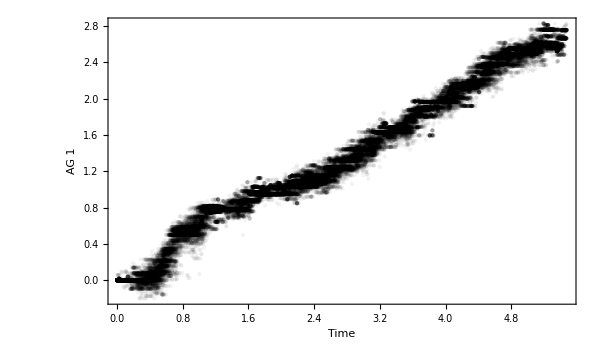

```mathematica
fig=ListPlot[timeAG1,AspectRatio->0.6,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.05]],FrameLabel->{"Time","AG 1"}]
```

```mathematica
tallies=Tally[AG1AG2];
```

```mathematica
Dimensions[tallies]
```

{4232,2}

```mathematica
points=Map[{PointSize[N[0.001*Sqrt[#[[2]]]]],Point[#[[1]]]}&,tallies];
```

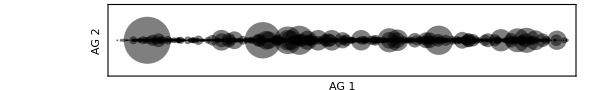

```mathematica
fig=Graphics[{Opacity[0.5],points},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False},FrameTicks->frameTicks]
```

```mathematica
jitter=Flatten[Map[Table[#[[1]]+RandomVariate[NormalDistribution[0,0.017],2],{Round[0.02*#[[2]]]}]&,tallies],1];
```

```mathematica
Length[jitter]
```

923

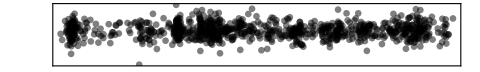

```mathematica
fig=ListPlot[jitter,AspectRatio->aspectRatio,PlotRange->plotRange,PlotStyle->Directive[PointSize[0.01],Black,Opacity[0.5]],GridLines->{Range[-10,10,gridWindow],Range[-10,10,gridWindow]},GridLinesStyle->GrayLevel[0.9],Frame->True,ImageSize->imageSize*0.8,FrameTicks->None]
```

```mathematica
Export["map.pdf",fig,"PDF"]
```

map.pdf

colorlist = Table[ColorData["Rainbow"][i/Ceiling[endTime]], {i, 0, Floor[endTime]}];

timeAG1AG2 = Map[{#[[1]], #[[2, 1]], #[[2, 2]]} &, data];

points = Cases[Map[{colorlist[[Ceiling[#[[1]]]]], Point[#[[{2, 3}]]]} &, timeAG1AG2], {RGBColor[__], _}];

fig = Graphics[{Directive[PointSize[Medium], Opacity[0.5]], points}, AspectRatio -> 0.6, PlotRange -> All, FrameLabel -> {"AG 1", "AG 2"}, Frame -> {True, True, False, False}];

Export["tips.png", fig, "PNG", ImageResolution -> 300]

## Trait history

```mathematica
history=Import["out.paths","Table"];
```

```mathematica
Length[history]
```

2952

```mathematica
getBranch[index_]:=Select[ToExpression[history[[index]]],#[[2]]==0&][[All,{1,3}]];
```

```mathematica
getTrunk[index_]:=Select[ToExpression[history[[index]]],#[[2]]==1&][[All,{1,3}]];
```

```mathematica
interval=1;
```

```mathematica
Length[Range[1,Length[history],interval]]
```

2952

```mathematica
branches=Table[getBranch[i],{i,1,Length[history],interval}];
```

```mathematica
trunks=Table[getTrunk[i],{i,1,Length[history],interval}];
```

```mathematica
tips=Table[If[Length[branches[[i]]]>0,branches[[i,1]],{}],{i,1,Length[history],interval}];
```

branchLines = {Directive[GrayLevel[0.3], Opacity[0.1]], Map[Line[Transpose[{#[[All, 1]], #[[All, 2, 1]]}]] &, branches]};

trunkLines = {Directive[Red, Opacity[0.1]], Map[Line[Transpose[{#[[All, 1]], #[[All, 2, 1]]}]] &, trunks]};

tipPoints = {Directive[GrayLevel[0.4], Opacity[1]], Map[Point, Cases[tips, {x_, {y_, z_}} -> {x, y}]]};

fig = Graphics[{branchLines, trunkLines, tipPoints}, ImageSize -> 600, AspectRatio -> 0.6, PlotRange -> All, Frame -> {True, True, False, False}, FrameLabel -> {"Time", "AG 1"}];

Export["paths1D.png", fig, "PNG", ImageResolution -> 300]

### 2D with branch thickness

```mathematica
branchScale=0.001;tipScale=0.005;clip=0.005;
```

```mathematica
xyBranches=Map[#[[All,2]]&,branches];
```

```mathematica
xyPairs=Tally[Flatten[Map[Partition[DeleteDuplicates[#],2,1]&,xyBranches],1]];
```

```mathematica
xyBranchLines=Map[{Thickness[Clip[branchScale*N[Sqrt[#[[2]]]],{0,clip}]],Line[#[[1]]]}&,xyPairs];
```

```mathematica
xyBranches=Map[#[[All,2]]&,trunks];
```

```mathematica
xyPairs=Tally[Flatten[Map[Partition[DeleteDuplicates[#],2,1]&,xyBranches],1]];
```

```mathematica
xyTrunkLines=Map[{Thickness[Clip[branchScale*N[Sqrt[#[[2]]]],{0,clip}]],Line[#[[1]]]}&,xyPairs];
```

```mathematica
xyPairs=Tally[Cases[tips,{x_,{y_,z_}}->{y,z}]];
```

```mathematica
xyPoints=Map[{PointSize[N[tipScale*Sqrt[#[[2]]]]],Point[#[[1]]]}&,xyPairs];
```

```mathematica
branchLines={CapForm["Round"],Directive[GrayLevel[0.3],Opacity[1]],xyBranchLines};
```

```mathematica
trunkLines={CapForm["Round"],Directive[Red,Opacity[1]],xyTrunkLines};
```

```mathematica
tipPoints={Directive[Black,Opacity[0.5]],xyPoints};
```

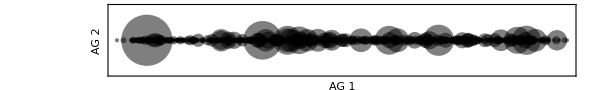

```mathematica
fig=Graphics[tipPoints,AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False},FrameTicks->frameTicks]
```

```mathematica
Export["tips.pdf",fig,"PDF"]
```

tips.pdf

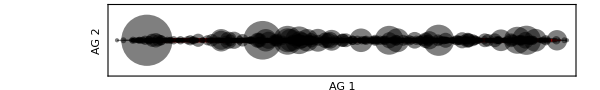

```mathematica
fig=Graphics[{branchLines,trunkLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False},FrameTicks->frameTicks]
```

```mathematica
Export["paths.pdf",fig,"PDF"]
```

paths.pdf